Cargamos librería - Configuramos

```mathematica
Get["C:\\Universidad\\PRM\\PRM_22_23\\Practica 2\\drawTxPRM.m"]
```

```mathematica
?drawTxPRM`*
```

```mathematica
SetIniParDraw[0.01,0.002]
```

Definimos funciones iniciales

```mathematica
Fifo[arr_,serv_]:=Module[{n,time},n=0;time=arr[[1]];
Map[(n++;If[time>=#,time+=serv[[n]],time=#+serv[[n]]])&,arr]]
```

```mathematica
ExpRnd[rate_]:=-Log[RandomReal[]]/rate //N
```

Calculamos tiempos

```mathematica
landa=80;
mu=100;
nm=1000;
```

```mathematica
Interarrivals=Table[ExpRnd[landa],nm];
Arrivals=Accumulate[Interarrivals];
```

```mathematica
Service=Table[ExpRnd[mu],nm];
```

```mathematica
Departures=Fifo[Arrivals,Service];
```

```mathematica
Injections=Departures-Service;
```

```mathematica
listaPaquetes=Table[{Injections[[n]],Service[[n]],n,0,0},{n,1,nm}];
```

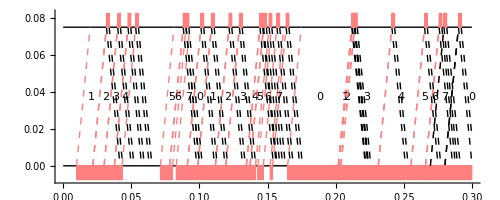

```mathematica
Show[DrawWin[0,0.3,8],Map[(DrawPacketTx[#])&,listaPaquetes]]
```

```mathematica
Manipulate[Show[DrawWin[ori,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[listaPaquetes]]],{ori,0,0.5-ww},{ww,0.1,0.5,0.1}]
```

```mathematica
ThrughtPut[lst_]:=Last[lst][[3]]/Last[lst][[1]]//N
```

```mathematica
ThrughtPut[listaPaquetes]
```

79.0173

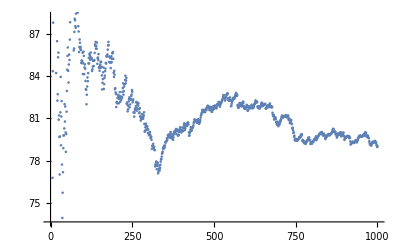

```mathematica
ListPlot[Map[(#[[3]]/#[[1]])&,listaPaquetes]]
```

```mathematica
Delay[lst1_,lst2_]:=Mean[lst2-lst1]
```

```mathematica
Delay[Arrivals,Injections]
```

0.0275862